```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/lehmann/results/nrqcd/2019-05-13/16/free

```mathematica
data = Import["mesoncorrelator_3s1.txt","Table"];
```

```mathematica
t=MapThread[#1&,{data[[2;;,1]]}];
c=MapThread[#1+I*#2&,{data[[2;;,2]],data[[2;;,3]]}];
retc=MapThread[{#1,#2}&,{data[[2;;,1]],data[[2;;,2]]}];
imtc=MapThread[{#1,#2}&,{data[[2;;,1]],data[[2;;,3]]}];
```

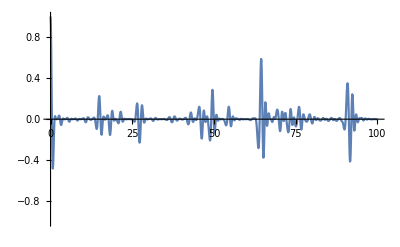

```mathematica
ListLinePlot[imtc,PlotRange->{All,{-1,+1}}]
```

```mathematica
dt=0.1
```

0.1

```mathematica
ftcor=Table[{w+I*w,0.5*dt*c[[1]]+0.5*dt*c[[-1]]*Exp[I*w*Length[c]*dt]+dt*Sum[c[[i]]*Exp[I*w*(i-1)*dt],{i,2,Length[c]-1}]},{w,-Pi/dt,+Pi/dt,2*Pi/dt/Length[c]}];
```

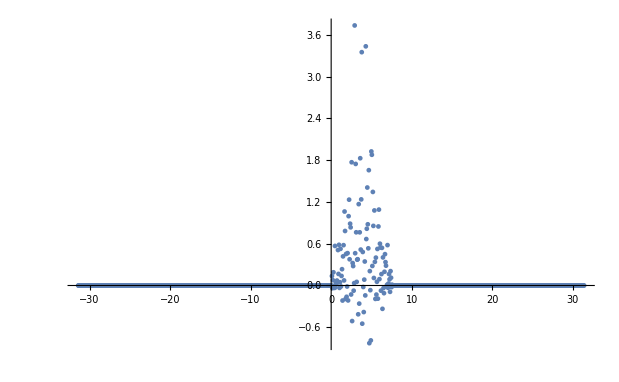

```mathematica
ListPlot[Im[ftcor],PlotRange->All]
```

```mathematica
d=c[[1;;100]];
```

100

```mathematica
ftc[x_]:=Table[{w+I*w,0.5*dt*x[[1]]+0.5*dt*x[[-1]]*Exp[I*w*Length[x]*dt]+dt*Sum[x[[i]]*Exp[I*w*(i-1)*dt],{i,2,Length[x]-1}]},{w,-Pi/dt,+Pi/dt,2*Pi/dt/Length[x]}];
```

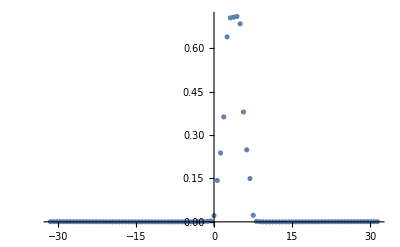

```mathematica
ftcorshort=ftc[c[[1;;100]]];ListPlot[Im[ftcorshort],PlotRange->All]
```

```mathematica
outtable[x_]:=Table[{Re[x[[i,1]]],Re[x[[i,2]]],Im[x[[i,2]]]},{i,1,Length[x]}];
```

```mathematica
ot=outtable[ftcorshort];
```

```mathematica
Export["spectrum_3s1.txt",ot,"Table"]
```

spectrum_3s1.txt